```mathematica
x=-2
y=x^3+6x^2-15x-20
```

-2

26

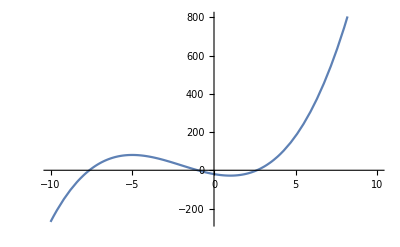

```mathematica
Plot[x^3+6x^2-15x-20,{x,-10,10},AxesStyle->Arrowheads[0.04]]
```

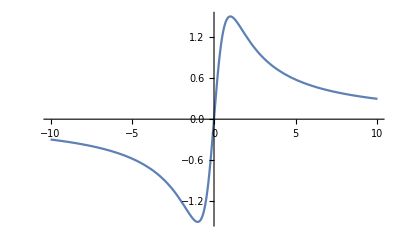

```mathematica
Plot[3*x/(1+x^2),{x,-10,10},AxesStyle->Arrowheads[0.04]]
```

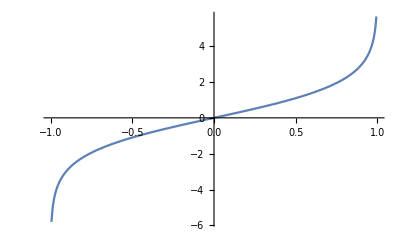

```mathematica
Plot[Log[(1+x)/(1-x)],{x,-1,1},AxesStyle->Arrowheads[0.04]]
```

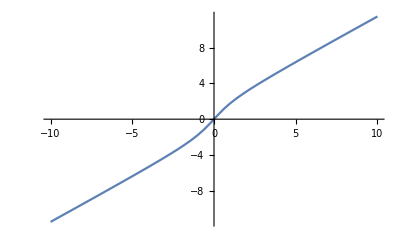

```mathematica
Plot[x+ArcTan[x],{x,-10,10},AxesStyle->Arrowheads[0.04]]
```

```mathematica
n=6
R=4000^(1/12)*(Log[4000])^(n+1)/((n+1)!)/(12^(n+1))
N[R]
```

6

Log[4000]^7/(18059231232 2^(7/12) 5^(3/4))

0.0000298427

```mathematica
Sum[(Log[4000])^i/i!/12^i,{i,0,6}]
```

1+Log[4000]/12+Log[4000]^2/288+Log[4000]^3/10368+Log[4000]^4/497664+Log[4000]^5/29859840+Log[4000]^6/2149908480

```mathematica
N[%]
```

1.99603

```mathematica
n=2
R=1/(n+1)*0.02^(n+1)
```

2

2.66667×10^-6

```mathematica
Sum[(-1)^(i-1)/i*0.02^i,{i,1,2}]
```

0.0198